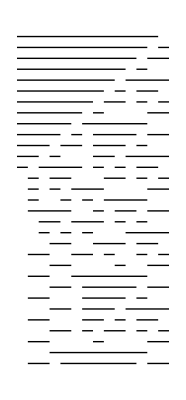

```mathematica
(* Create a Sequence of 30 zeros *)
list = Table[0, {30}];
(*Add a one right in the middle*)
list[[15]] = 1;
(*Define our rule table for Rule 110 (1101110)*)
rules = {
{0,0,0} -> 0,
{0,0,1} -> 1, 
{0,1,0} -> 1, 
{0,1,1} -> 1, 
{1,0,0} -> 0, 
{1,0,1} -> 1,
{1,1,0} -> 1,
{1,1,1} -> 0
};
(*Chop up the list and apply the rules*)
Partition[list, 3, 1] /. rules;
(*Pad the list with zeros on both sides*)
Join[{0}, list, {0}];
(*Create a function to do this*)
step[seq_] := Join[{0}, Partition[seq, 3, 1] /. rules, {0}];
array = NestList[step, list, 30];
ArrayPlot [array];
lines = {};

For[i = 1, i≤ Length[array], ++i,
	(* row i *)
	line = {};
	For[j=1, j≤ Length[array[[i]]], ++j,
		(*Print[line, " ", i," ", j];*)
		If[Length[line] == 0, (* init *)
			line = {i,j,i,j, array[[i,j]]}, 
		(*else: if value is the same as last line's value*)
			(*Print["not null so -->"];*)
			If[array[[i,j]] == line[[5]],
				line = {line[[1]], line[[2]], i,j, line[[5]]},
				(*else: new value --> store old line, start new line*)
				lines = Append[lines, line]; line = {i,j,i,j,array[[i,j]]}]
		]
	]
]
(*subarray = array[[6]];
Position[subarray, 1];*)
SubArrayToLine[a_] := (
	p1 = {a[[2]], -a[[1]]};
	p2 = {a[[4]], -a[[3]]};
	l = Line[{p1, p2}];
	Return[l];
)
properLines = {};
For[k = 1, k ≤ Length[lines],++k,
	(*Print[lines[[k]]];*)
	properLines = Append[properLines, SubArrayToLine[lines[[k]]]];
]

Graphics[{
	properLines
}]

(*Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Black,Dashed,Line[{{-1,0},{4,0}}]}]*)
```